```mathematica
M={{1,2,3},{1,2,3},{7,8,9}}
ID= IdentityMatrix[3]; ID//MatrixForm
```

{{1,2,3},{1,2,3},{7,8,9}}

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Information[RandomSample]
```

```mathematica
orthoChain[Q0_, m_, L_]:= Module[{dummyP, theta, Eij, l,K, sign},
If [OrthogonalMatrixQ[Q0]==False,Print["Initial matrix is NOT orthogonal."]; Return[Q0//MatrixForm], Nothing];
dummyP = Q0;
Table[
theta = RandomReal[{0,2*Pi}]; 
{i,j}= RandomSample[Range[1,m],2]  ;
Eij = IdentityMatrix[m];
Eij[[i,i]] = Cos[theta];
Eij[[j,j]] =  Cos[theta];
Eij[[i,j]] = Sin[theta];
Eij[[j,i]] = -Sin[theta];
{l} = RandomSample[{i,j},1];
{sign}= RandomSample[{-1,1},1];
Eij[[l,;;]] = sign*Eij[[l,;;]];
dummyP = Eij.dummyP;
dummyP
,{ii, 1, L}]
]
```

```mathematica
Map[MatrixForm,orthoChain[ID,3, 5]]
```

{(-0.207618 | 0. | 0.97821
0. | 1. | 0.
0.97821 | 0. | 0.207618),(-0.43333 | 0. | -0.901235
0. | 1. | 0.
-0.901235 | 0. | 0.43333),(-0.267258 | 0.787156 | -0.555841
0.341098 | 0.616755 | 0.709412
-0.901235 | 0. | 0.43333),(0.422982 | 0.217229 | 0.879714
-0.0941318 | 0.976121 | -0.195774
-0.901235 | 0. | 0.43333),(0.422982 | 0.217229 | 0.879714
-0.830543 | -0.29526 | 0.472249
0.362331 | -0.930394 | 0.0555281)}

```mathematica
orthoChain2[Q0_, m_, L_]:= Module[{dummyP, Eij, l, sign,K},
Clear[theta];
If [OrthogonalMatrixQ[Q0]==False,Print["Initial matrix is NOT orthogonal."]; Return[Q0//MatrixForm], Nothing];
dummyP = Q0;
Table[
{i,j}=RandomSample[Range[1,m],2];
Eij = IdentityMatrix[m];
Eij[[i,i]] = Cos[theta];
Eij[[j,j]] = Cos[theta];
Eij[[i,j]] = Sin[theta];
Eij[[j,i]] = -Sin[theta];
{l} = RandomSample[{i,j},1];
{sign}= RandomSample[{-1,1},1];
Eij[[l,;;]] = sign*Eij[[l,;;]];
dummyP = Eij.dummyP;
dummyP//Tr
,{ii, 1, L}]
]
```

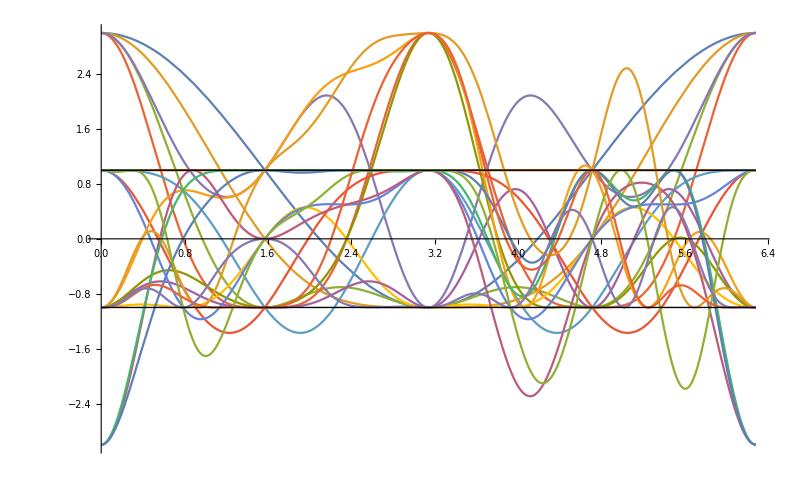

```mathematica
return = orthoChain2[ID, 3, 20];
Plot[return,{theta, 0,2* Pi}, Epilog->{Line[{{0,-1},{2*Pi,-1}}],Line[{{0,1},{2*Pi,1}}]}]
```

```mathematica
return =orthoChain2[ID, 3, 5]; return//TableForm
```

1+2 Cos[theta]
2 Cos[theta]+Cos[theta]^2
Cos[theta]+Cos[theta]^2+Cos[theta]^3-Sin[theta]^2-Cos[theta] Sin[theta]^2
Cos[theta]^2+Cos[theta]^3-Sin[theta]^2+Cos[theta] (Cos[theta]^2-Cos[theta] Sin[theta]^2)
Cos[theta]^2-Sin[theta]^3+Sin[theta] (-Cos[theta] Sin[theta]-Cos[theta]^2 Sin[theta])+Cos[theta] (Cos[theta]^3-Sin[theta]^2)-Sin[theta] (-Cos[theta] Sin[theta]^2+Cos[theta] (Cos[theta] Sin[theta]+Cos[theta]^2 Sin[theta]))+Cos[theta] (Sin[theta]^3+Cos[theta] (Cos[theta]^2-Cos[theta] Sin[theta]^2))

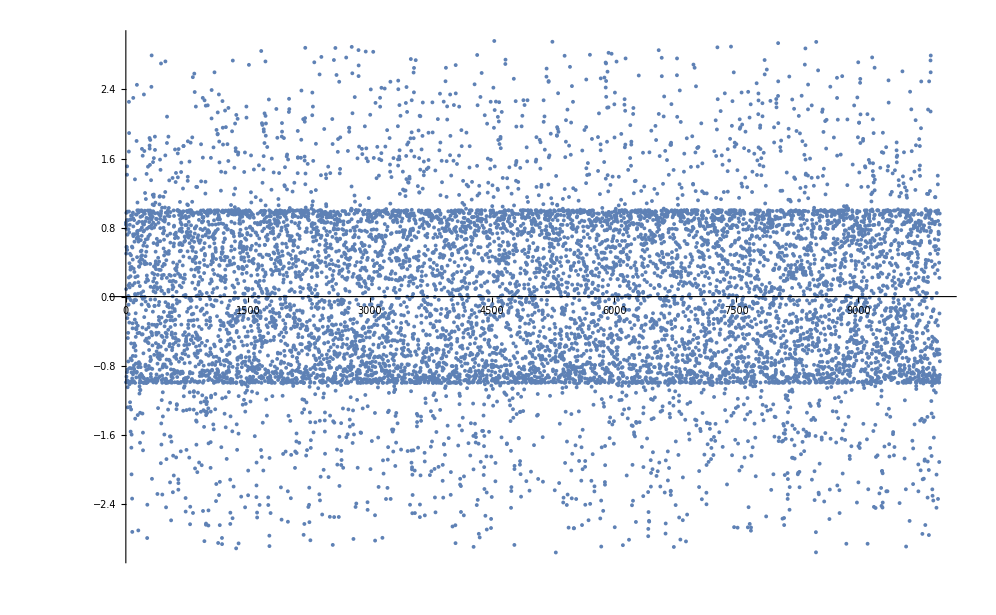

```mathematica
Map[Tr,orthoChain[ID,3, 10000]]//ListPlot
```

```mathematica
simulation =Parallelize[Table[Map[Tr,orthoChain[ID,3, 10000]]//Mean,{1000}]];
```

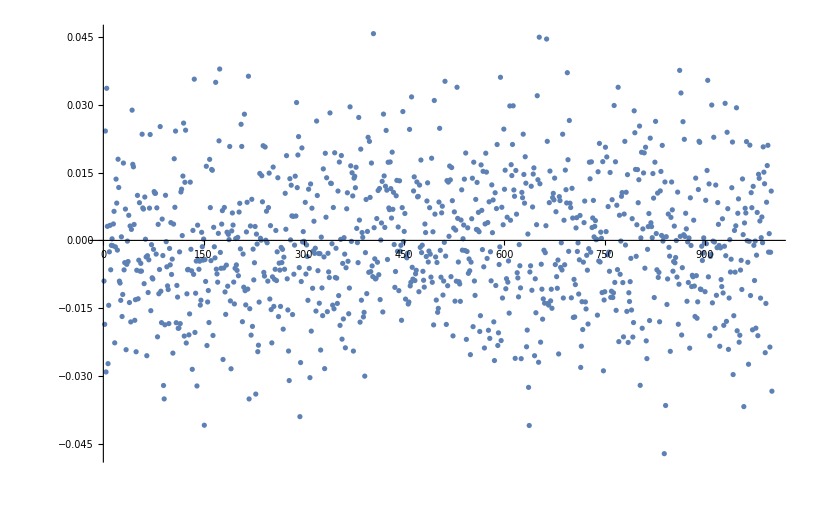

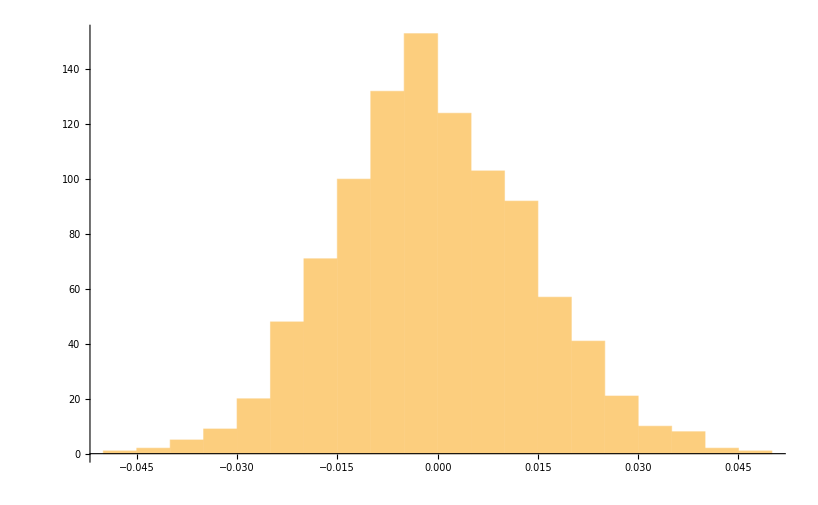

```mathematica
ListPlot[simulation]
Histogram[simulation]
```

```mathematica
ListPointPlot3D[Map[Diagonal,orthoChain[ID,3, 10000]]]
```

-Graphics3D-